## Set up the models and the standard parameters

The goal here is to re-connect the ideas of the models and the parameters we had before to try and think about some implied landscape where we can see what the distribution is of the probability that some organisms will end up using the same space on a landscape.

```mathematica
(*Define constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*adjust for larger or smaller landscapes*)

(*Generate random values for T and S across the grid*)
Tgrid=RandomVariate[NormalDistribution[20,0.5],gridSize];
Sgrid=RandomVariate[GammaDistribution[2,1],gridSize];

(*Compute probabilities w_{i,j} across the landscape*)
(*Truncate landscape probabilities to be>=0*)landscapeProbabilities=Table[Max[0,w[Tgrid[[i,j]],Sgrid[[i,j]]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];
```

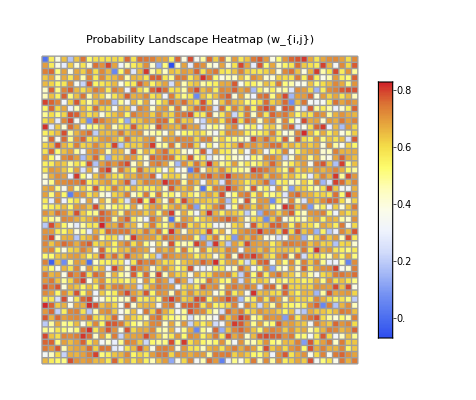

```mathematica
(*Plot as a heatmap*)
heatmap=ArrayPlot[landscapeProbabilities,ColorFunction->"TemperatureMap",Mesh->True,PlotLabel->"Probability Landscape Heatmap (w_{i,j})",
PlotLegends->Automatic];
heatmap
```

```mathematica
(*Flatten the landscape probabilities for density plot*)
flatProbabilities=Flatten[landscapeProbabilities];

(*Plot as a density plot*)
densityPlot=DensityPlot[Evaluate[PDF[KernelMixtureDistribution[flatProbabilities,"Silverman"],x]],{x,Min[flatProbabilities],Max[flatProbabilities]},PlotRange->All,Filling->Axis,PlotLabel->"Probability Density Plot (w_{i,j})",AxesLabel->{"w_{i,j}","Density"}];

(*Display both plots*)
Column[{heatmap,densityPlot}]
```

ArrayPlot::optx: Unknown option ColorBar→True in ArrayPlot[{«1»}].

DensityPlot::argrx: DensityPlot called with 2 arguments; 3 arguments are expected.

ArrayPlot[{{0.59858,0.540828,0.359858,0.598351,0.646489,0.637084,0.587494,0.646617,0.435044,0.579632,0.537516,0.486178,0.641557,0.623759,0.585666,0.593922,0.636737,0.388599,0.473648,0.411976,0.147917,0.435172,0.488951,0.611715,0.404875,0.608128,0.323303,0.632338,0.499539,0.586411,0.519824,0.511791,0.577739,0.375362,0.208192,0.651415,0.17153,0.530926,0.594881,0.577693,0.549875,0.603329,0.609118,0.61276,0.509507,0.579166,0.0313453,0.502125,0.261533,0.432263},{0.629432,0.612072,0.0448284,0.598942,0.63901,0.520514,0.570333,0.103035,0.577443,0.580311,0.573185,0.619945,0.185212,0.554012,0.605296,0.552475,0.654168,0.602459,0.381642,0.529697,0.43763,0.530776,0.60692,0.414531,0.45485,0.435173,0.632201,0.507917,0.542177,0.631727,0.61081,0.640264,0.23847,0.344826,0.604709,0.594677,0.427362,0.545647,0.427987,0.638798,0.392478,0.508533,0.580559,0.0702601,0.604416,0.590725,0.651882,0.624224,0.416566,0.394117},{0.556917,0.617937,0.137611,0.571921,0.603422,0.622879,0.58974,0.0794015,0.615931,0.484386,0.239322,0.597627,0.648596,0.467385,0.355031,0.631958,0.541616,0.564842,0.520137,0.596504,0.578241,0.565086,0.64568,0.619994,0.356866,0.364947,0.598659,0.604345,0.64724,0.217647,0.618534,0.503436,0.587571,0.643594,0.484618,0.541201,0.0622645,0.607072,0.548716,0.619475,0.460306,0.611363,0.557962,0.363447,0.109928,0.556251,0.283885,0.603919,0.595493,0.604493},{0.558816,0.400037,0.605763,0.54875,0.290585,0.529605,0.55739,0.452399,0.0725868,0.637394,0.616834,0.462513,0.634858,0.596453,0.629776,0.551255,0.611229,0.581015,0.672579,0.618391,0.584341,0.529451,0.486801,0.212874,0.306874,0.622258,0.646355,0.615125,0.645165,0.519652,0.572994,0.543097,0.438826,0.440279,0.618502,0.492674,0.441476,0.625789,0.555899,0.265299,0.625059,0.462266,0.555145,0.492463,0.622738,0.632864,0.576037,0.659974,0.613385,0.442557},{0.598482,0.573186,0.627954,0.319781,0.583707,0.611641,0.586489,0.605782,0.53393,0.542192,0.522342,0.611512,0.512974,0.606114,0.554431,0.497398,0.49777,0.458352,0.554422,0.482974,0.592606,0.62521,0.592735,0.178998,0.594192,0.534337,0.610591,0.60974,0.328854,0.612508,0.576224,0.607288,0.588728,0.579799,0.601214,0.557589,0.137686,0.579238,0.522379,0.642776,0.590329,0.501684,0.603966,0.614998,0.594759,0.365995,0.588766,0.554525,0.640924,0.508178},{0.168278,0.656515,0.479824,0.605884,0.608921,0.621891,0.568274,0.44108,0.439101,0.606387,0.599218,0.623116,0.609956,0.518569,0.453487,0.530519,0.593658,0.548833,0.315811,0.133135,0.652366,0.564416,0.286368,0.600711,0.564742,0.569464,0.487127,0.380763,0.48366,0.653869,0.418694,0.635744,0.587017,0.60913,0.416752,0.626155,0.479013,0.411573,0.363697,0.635559,0.61622,0.457548,0.537885,0.419334,0.319831,0.523616,0.614093,0.597146,0.35285,0.441809},{0.550421,0.606357,0.523615,0.581244,0.110543,0.273158,0.387058,0.609958,0.539157,0.617989,0.652506,0.647868,0.611053,0.595325,0.459364,0.649203,0.598679,0.553467,0.449461,0.402253,0.605713,0.536047,0.575925,0.323391,0.591889,0.554986,0.611379,0.579901,0.583268,0.635168,0.425274,0.0285051,0.571221,0.598574,0.571426,0.316336,0.646313,0.431878,0.294591,0.623816,0.652063,0.621767,0.387667,0.33647,0.600904,0.62855,0.511613,0.629521,0.168129,0.576867},{0.470161,0.637638,0.614553,0.654716,0.636139,0.56258,0.450152,0.291566,0.628973,0.27807,0.139208,0.575765,0.564119,0.518447,0.5984,0.377624,0.0481775,0.611765,0.599079,0.611067,0.557332,0.195687,0.576356,0.416393,0.672367,0.448597,0.414114,0.39687,0.349829,0.633305,0.326091,0.623869,0.633259,0.658692,0.0698787,0.657355,0.326954,0.337905,0.565888,0.593791,0.585338,0.622331,0.599205,0.491978,0.449508,0.272213,0.468956,0.183873,0.64382,0.65536},{0.145577,0.56336,0.531516,0.487052,0.643268,0.4175,0.458315,0.644482,0.625682,0.64066,0.5765,0.606229,0.471366,0.533672,0.601184,0.4557,0.611372,0.572424,0.641912,0.587376,0.645203,0.609652,0.566405,0.207898,0.500101,0.627676,0.522898,0.553891,0.634055,0.592227,0.52798,0.595106,0.558003,0.5383,0.619696,-0.00376623,0.571699,0.645552,0.331636,0.589365,0.295475,0.499503,0.633234,0.541695,0.625937,0.466921,0.559286,0.554801,0.0831821,0.473411},{0.422017,0.441329,0.547933,0.496563,0.596907,0.241246,0.587244,0.549762,0.362132,0.574111,0.488419,0.634111,0.356027,0.618864,0.33249,0.631257,0.519353,0.609577,0.0667531,0.551455,0.62699,0.437845,0.638053,0.606149,0.313038,0.46456,0.594672,0.339464,0.615281,0.588734,0.498475,0.350893,0.197406,0.535439,0.411455,0.42134,0.548953,0.606402,0.51031,0.593456,0.484024,0.565188,0.572067,0.631528,0.576004,0.322198,0.147555,0.514171,0.43355,0.633015},{0.570425,0.656537,0.469014,0.583539,0.612795,0.461151,0.619281,0.342954,0.613997,0.43067,0.577421,0.596832,0.432229,0.600757,0.607008,0.448897,0.548314,0.632889,0.604877,0.568435,0.634255,0.624375,0.528264,0.607711,0.361739,0.574241,0.511052,0.613943,0.625228,0.666657,0.518744,0.453617,0.332786,0.435811,0.586992,0.501189,0.672305,0.641463,0.604799,0.293972,0.472647,0.389575,0.658387,0.311951,0.594367,0.594688,0.451247,0.61025,0.600369,0.568423},{0.627364,0.485878,0.48073,0.620002,0.675506,-0.213332,0.448221,0.624031,0.233673,0.603227,0.581119,0.380532,0.547406,-0.167689,0.450764,0.603303,0.210674,0.483703,0.561097,0.418893,0.647343,0.471806,0.540808,0.394724,0.397945,0.581535,0.554861,0.4199,0.584303,0.471884,0.614723,0.586655,0.471014,0.651842,0.609261,0.40049,0.0525871,0.169632,0.593727,0.623864,0.309252,0.611285,0.609916,0.619181,0.569069,0.586289,0.631055,0.57221,0.561784,0.55704},{0.612615,0.544599,0.498747,0.563625,0.407747,0.590056,0.578481,0.453254,0.414936,0.481404,0.163184,0.32629,0.616661,0.400073,0.351159,0.447567,0.516661,0.609206,0.577747,0.579333,0.466976,0.641039,0.603714,0.513068,0.257129,0.25038,0.635122,0.622408,0.523989,0.418235,0.597365,0.556514,0.590896,0.617869,0.261677,0.544412,0.605731,0.570109,0.626229,0.60201,0.646597,0.509341,0.516988,0.182325,0.588793,0.538572,0.316538,0.599584,0.184746,0.596275},{0.473802,0.579921,0.577004,0.637606,0.518258,-0.0431693,0.523467,0.441016,0.590605,0.572859,0.368727,0.517475,0.625578,0.604607,0.605933,0.540785,0.617681,0.612143,0.623642,0.557028,0.652002,0.434489,0.618862,0.524658,0.598944,0.415012,0.642461,0.613676,0.442526,0.353882,0.0475239,0.492201,0.556703,0.595876,0.539821,0.529195,0.413626,0.553136,0.371851,0.582533,0.615736,0.466963,0.491098,0.632302,0.550845,0.252723,0.648029,0.362265,0.218933,0.631116},{0.53962,0.667719,0.357804,0.539783,0.609538,0.209989,0.512437,0.267981,0.532751,0.534729,0.664213,0.418114,0.440991,0.258501,0.433634,0.457361,0.349777,0.429287,0.632817,0.614408,0.59886,0.557802,0.540022,0.616428,0.172309,0.603245,0.549007,0.533908,0.430411,0.63406,0.419144,0.520953,0.572627,0.625611,0.638402,0.621158,0.54179,0.633509,0.530014,0.482652,0.636097,0.327536,0.631824,0.567609,0.597769,0.00421677,0.539178,0.577021,0.552148,0.615794},{0.453554,0.569386,0.636929,0.370314,0.297579,0.646726,0.627675,0.626599,0.585271,0.409742,0.552439,0.32436,0.636988,0.286454,0.512699,0.41389,0.151315,0.594267,0.585093,0.50202,0.426202,0.354968,0.561031,0.399495,0.41178,0.574782,0.301389,0.529957,0.629863,0.663611,0.641987,0.603589,0.427008,0.50697,0.418132,0.596648,0.43678,0.62685,0.669658,0.556006,0.427288,0.634884,0.566804,0.631421,0.524425,0.583316,0.427589,0.587481,0.513248,0.558674},{0.535721,0.621506,0.492142,0.385033,0.596233,0.604142,0.493777,0.410632,0.636098,0.597215,0.168438,0.554872,0.605344,0.575355,0.572247,0.435186,0.488669,0.539176,0.581309,-0.125412,0.503745,0.21713,0.58623,0.584639,0.56531,0.633603,0.604851,0.552844,0.568968,0.650156,0.603042,0.463028,0.638778,0.551894,0.424473,0.608592,0.486987,0.634359,0.658956,0.596668,0.436531,0.233881,0.586352,0.565624,0.613531,0.263098,0.49211,0.563739,0.594435,0.588264},{0.220057,0.648659,0.166149,0.282334,0.54221,0.613588,0.581562,0.497623,0.587072,0.571875,0.615717,0.630325,0.530908,0.547964,0.560523,0.63933,0.638471,0.621196,0.595664,0.384746,0.643265,0.522851,0.488312,0.266451,0.553227,0.417344,0.634054,0.434801,0.33753,0.0653806,0.620829,0.645877,0.612465,0.607516,0.594735,0.604179,0.651507,0.560487,0.547406,0.637517,0.597643,0.60608,0.320063,0.328461,0.539729,0.592927,0.350564,0.553465,0.569317,0.607772},{0.356726,0.368764,0.611255,0.538689,0.654837,0.512947,0.657478,0.524002,0.524447,0.251731,0.60511,0.572168,0.606455,0.641998,0.510181,0.553421,0.583535,0.531038,0.633045,0.469082,0.529925,-0.158226,0.529193,0.450033,0.551948,0.596507,0.178925,0.595136,0.306953,0.543696,0.628186,0.574124,0.592701,0.620885,0.590292,0.411103,0.219826,0.513604,0.366935,0.663698,0.263165,0.55511,0.632226,0.664375,0.427564,0.669008,0.618778,0.520254,0.449155,0.623404},{0.62155,0.636077,0.479087,0.477677,0.609639,0.553262,0.537199,0.433863,0.528262,0.630298,0.53483,0.570297,0.584508,0.485809,0.343871,0.612517,0.521914,0.334696,0.670357,0.585804,0.625953,0.624025,0.573792,0.462849,0.600504,0.230459,0.61825,0.636309,0.650417,0.618195,0.513176,0.614256,0.585207,0.423186,0.0244556,0.630572,0.635027,0.414622,0.642289,0.54005,0.64739,0.646331,0.558031,0.568526,0.316142,0.565911,0.605911,0.4807,0.572935,0.617594},{0.623264,0.534384,0.505931,0.669883,0.325582,0.605424,0.439198,0.401882,0.658683,0.580957,0.624465,0.556313,0.58176,0.479683,0.579078,0.629992,0.332827,0.62122,0.546121,0.578907,0.443198,0.341002,0.653102,0.500343,0.608846,0.551413,0.542004,0.553531,0.413501,0.60687,0.617401,0.343799,0.565918,0.408262,0.624143,0.499572,0.640461,0.588572,0.633708,0.383325,0.404794,0.643647,0.526273,0.409436,0.592109,0.048813,0.633122,0.283557,0.573121,0.631907},{0.580176,0.470161,0.617889,0.5916,0.456048,0.64769,0.536676,0.459421,0.440306,0.206606,0.573471,0.6076,0.495826,0.633534,0.291458,0.616391,0.609613,0.583427,0.297175,0.578595,0.616675,0.581187,0.669211,0.351622,0.489037,0.573283,0.510909,0.548361,0.460649,0.615911,0.603272,0.547907,0.29587,0.481473,0.566431,0.585187,0.464874,0.578485,0.562455,0.606939,0.587536,0.573411,0.637547,0.476699,0.577891,0.572436,0.631153,0.595026,0.407712,0.396701},{0.615332,0.66004,0.399622,0.61324,0.234756,0.584243,0.44716,0.444884,-0.015884,0.355705,0.623275,0.60832,0.642944,0.342824,0.436814,0.612515,0.645681,0.441704,0.62783,0.662237,0.578401,0.668089,0.49115,0.6329,0.593736,0.510647,0.329531,0.269492,0.382433,0.4234,0.611251,-0.0703168,0.311817,-0.221953,0.638665,0.453745,0.607918,0.635456,0.427222,0.454925,0.597019,0.629442,0.649732,0.61436,0.636403,0.625496,0.556018,0.575752,0.62085,0.458659},{0.570812,0.617781,0.579576,0.0545764,0.614801,0.513383,0.658337,0.33638,0.535914,0.619748,0.561216,0.573707,0.642666,0.653308,0.466667,0.572691,0.60401,0.526951,0.557828,0.634631,0.384124,0.50424,0.595584,0.656096,0.473509,0.456876,0.316637,0.0385368,0.533239,0.460476,0.5976,0.404753,0.621543,0.360166,0.616011,0.559267,0.638793,0.603991,0.559445,0.684386,0.503736,0.60718,0.661754,0.596733,0.507545,0.598211,0.642663,0.60106,0.383598,0.521446},{0.656272,0.566367,0.592244,0.488439,0.60517,0.517001,0.544731,0.608681,0.632227,0.628012,0.593516,0.299279,0.242417,0.433028,0.563727,0.169783,0.602636,0.586474,0.611616,0.130715,0.601975,0.582738,0.610454,0.496349,0.641019,0.572195,0.288897,0.610579,0.192528,0.60137,0.594396,0.349398,0.407169,0.170396,0.447223,0.642488,0.629436,0.609235,0.640431,0.486801,0.50683,0.4443,0.515594,0.249731,0.530436,0.319895,0.430956,0.630566,0.636757,0.634955},{0.347489,0.398047,0.530305,0.564835,0.519163,0.621134,0.653258,0.405295,0.462422,0.673381,0.597117,0.644347,0.637936,0.167354,0.397542,0.619517,0.625491,0.571515,0.609106,0.287131,0.478412,0.567104,0.532232,0.587381,0.582575,0.166834,0.579768,0.611594,0.62241,0.442297,0.639286,0.544698,0.114148,0.385022,0.641022,0.359944,0.568872,0.612407,0.545031,0.599224,0.541501,0.586294,0.448312,0.522255,0.439204,0.589746,0.577345,0.460237,0.109755,0.554219},{0.508776,0.385106,0.594169,0.619037,0.510778,0.593143,0.637163,0.593536,0.339219,0.613607,0.572921,0.609348,0.639057,0.314664,0.451484,0.555216,0.611436,0.654646,0.615064,0.622486,0.50136,0.57686,0.520689,0.610443,0.619533,0.633929,0.609546,0.627455,0.625796,0.544498,0.550894,0.532585,0.61889,0.550827,0.446216,0.618924,0.0190251,0.240439,0.638107,0.614999,0.618362,0.450386,0.498761,0.582898,0.449333,0.562866,0.606716,0.422638,0.415965,0.476443},{0.613679,0.526263,0.287553,0.653648,0.476901,0.412906,0.574727,0.617521,0.329095,0.44118,0.665064,0.652201,0.594875,0.603502,0.607376,0.0668883,0.500857,0.599451,0.454181,0.612185,0.582136,0.564428,0.400963,0.512554,0.345408,0.600169,0.648445,0.470876,0.417377,0.645175,0.55791,0.27778,0.575237,0.423143,0.573334,0.593488,0.540822,0.533673,0.358314,0.411,0.630094,0.609534,0.635544,0.231521,0.400253,0.634065,0.612097,0.624949,0.599914,0.576425},{0.59105,0.401395,0.510009,0.414136,0.0906144,0.575522,0.544763,0.60264,0.466069,0.572512,0.444369,0.615585,0.590511,0.611152,0.509547,0.376472,0.496071,0.595613,0.562449,0.598467,0.597575,0.60371,0.517078,0.395552,0.590198,0.446674,0.615811,0.597087,0.586574,0.500362,0.467201,0.547833,0.570627,0.561694,0.600883,0.64688,0.590326,0.659167,0.508328,0.664365,0.490943,0.672676,0.533445,0.456263,0.0722308,0.61697,0.0832826,0.603581,0.572872,0.482619},{0.547872,0.484395,0.634822,0.585098,0.431149,0.496533,0.630742,0.640767,0.382819,0.650062,0.488531,0.390762,0.491641,0.65489,0.573806,0.417859,0.459259,0.61595,0.273,0.515292,0.472097,0.581485,0.642631,0.479047,0.608323,0.666782,0.391492,0.62572,0.331389,0.105678,0.554826,0.596634,0.573625,0.341874,0.421956,0.649966,0.639476,0.249128,0.562639,0.573177,0.4429,0.593891,0.385945,0.452121,0.378623,0.626051,0.57359,0.631742,0.600159,0.580883},{0.450562,0.649819,0.230743,0.61924,0.600307,0.483383,0.576716,0.653493,0.437977,0.582347,0.638934,0.581922,0.585193,0.406193,0.234493,0.469718,0.499877,0.576104,0.383081,0.62419,0.391136,0.619759,0.546635,-0.0729931,0.580748,0.168583,0.64428,0.64691,0.463866,0.605914,0.596099,-0.0553814,0.360827,0.343164,0.680674,0.438005,0.526132,0.554881,0.528101,0.635341,0.645916,0.504333,0.52171,0.481364,0.0861314,0.60621,0.565851,0.0861268,-0.0208571,0.64204},{0.457733,0.0799219,0.628681,0.626043,0.622815,0.565652,0.317956,0.536873,0.51889,0.563669,0.619973,-0.25281,0.535992,0.622333,0.656825,0.333972,0.652738,0.618428,0.549969,0.612292,0.550485,0.431508,0.663317,-0.386366,0.623711,0.463139,0.608526,0.51402,0.50717,0.642038,0.422852,0.60961,0.654466,0.60577,0.549262,0.597811,0.612448,0.531858,0.6223,0.638261,0.417131,0.582326,0.468656,0.549511,0.602241,0.546921,0.565925,0.516432,0.469122,0.654705},{0.260171,0.614683,0.581139,0.618283,0.631202,0.634613,0.452336,0.52736,0.60601,0.659069,0.510575,0.380544,0.57943,0.317122,0.380901,0.515712,0.609952,0.556194,0.189456,0.579322,0.637487,0.56158,0.350656,0.522092,0.137218,0.404673,0.454406,0.0257016,0.297782,0.442757,0.608467,0.448232,0.645591,0.598172,0.615612,0.584464,0.60564,0.596846,0.358226,0.597204,0.607452,0.487286,0.642168,0.382323,0.618709,0.380611,0.519639,0.534137,0.546338,0.348675},{0.491212,0.56207,0.58525,0.300816,0.459313,0.543047,0.548268,0.614859,0.534804,0.65624,0.637177,0.523686,0.516103,0.671866,0.596083,0.593155,0.589588,0.47422,0.61109,0.530791,0.640781,0.588382,0.355018,0.602876,0.480686,0.54801,0.641366,0.618468,0.537449,0.624483,0.582221,0.51513,0.609872,0.544144,0.343002,0.528867,0.474858,0.471803,0.212085,0.639102,0.441567,0.493379,0.631845,0.309339,0.377359,0.607682,0.407306,0.30135,0.435703,0.447301},{0.626742,0.492172,0.600512,0.606285,0.163892,0.228333,0.555472,-0.00467297,0.549061,0.543788,-0.427954,0.344952,0.549787,0.253531,0.325026,0.43044,0.448918,0.644938,0.506406,0.540862,0.589792,0.547592,0.624383,0.580086,0.603046,0.602662,0.612841,0.632029,0.592115,0.497459,0.545362,0.414189,0.598611,0.46778,0.484598,0.661885,0.422965,0.625563,0.622803,0.38328,0.618772,0.635383,0.532227,0.384664,0.527623,0.207556,0.474591,0.589603,0.580189,0.206064},{0.590466,0.605602,0.229549,0.51091,0.616035,0.493726,0.459065,0.263541,0.594699,0.606928,0.628147,0.449234,0.641248,0.461903,0.632234,0.481281,0.598171,0.587256,0.510409,0.629895,0.601502,0.66485,0.447875,0.448638,0.0401025,0.484944,0.561622,0.499806,0.633718,0.565833,0.56885,0.645697,0.521526,0.365698,0.638951,0.520598,0.601349,0.409964,0.570642,0.589069,0.558208,0.395459,0.468067,0.541522,0.280252,0.415434,0.576734,0.545867,0.623714,0.232804},{0.408406,0.460417,0.445877,0.0913264,0.5193,0.567887,-0.0645879,0.637395,0.593186,0.457421,0.599713,0.181513,0.516451,0.516084,0.389424,0.604516,0.408931,0.451059,0.412088,0.627137,0.590971,0.560534,0.531004,0.243877,0.638932,0.601813,0.504408,0.404669,0.332353,0.597067,0.626633,0.570743,0.459468,0.633957,0.338271,0.557107,0.519457,0.54947,0.659523,0.666809,0.14075,0.633712,0.43391,0.621561,0.221519,0.452133,0.345725,0.627497,0.55712,0.5767},{0.485286,0.454918,0.644161,0.371482,0.387385,0.616244,0.601432,0.621806,0.371417,0.563596,0.623232,0.564022,0.506966,0.589703,0.58434,0.61817,0.468305,0.611775,0.477914,0.206798,0.56896,0.618471,0.664282,0.536315,0.634272,0.374262,0.658865,0.511151,0.629531,0.535409,0.415508,0.611567,0.631466,0.598515,0.208474,0.536076,0.430611,0.626515,0.522725,0.501723,0.641037,0.466558,0.258086,0.603471,0.652103,0.561017,0.178114,0.588894,0.146051,0.593408},{0.602487,0.398907,0.609522,0.59041,0.562989,0.417609,0.627133,0.546272,0.492572,0.528964,0.344173,0.576013,0.640097,0.641787,0.62813,0.557843,0.56733,0.63279,0.604207,0.315428,0.480977,0.582567,0.642053,0.564746,0.655317,0.588585,0.593856,0.622113,0.558793,0.160579,0.474405,0.598784,0.647946,0.468196,0.567798,0.245357,0.605407,0.618075,0.366348,0.647102,0.594565,0.439638,0.440148,0.609291,0.0607423,0.533695,0.514752,0.468789,0.60653,0.429595},{0.532473,0.637042,0.65241,0.595217,0.637477,0.570369,0.437274,0.588678,0.486144,0.511236,0.553852,0.514102,0.271727,0.529744,0.55366,0.491728,0.580573,0.470133,0.432594,0.286431,0.407183,0.543593,0.593881,0.348145,0.620664,0.597794,0.624507,0.266372,0.625162,0.659221,0.649031,0.620213,0.59413,0.50553,0.615545,0.514741,0.52516,0.410589,0.590487,0.411531,0.166827,0.560816,0.44358,0.599036,0.566023,0.637266,0.582172,0.596272,0.327245,0.663132},{0.241788,0.479329,0.570612,0.290754,0.626825,0.415799,0.538159,0.619202,0.555242,0.0764622,0.623811,0.595064,0.361244,0.429971,0.633316,0.585666,0.564368,0.596997,0.461928,0.541119,0.590566,0.637633,0.24043,0.164646,0.611439,0.511732,0.394041,0.191506,0.387965,0.507084,0.631575,0.629578,0.546536,0.611193,0.602298,0.46823,0.577484,0.643637,0.64438,0.580383,0.63906,0.425863,0.495002,0.460259,0.566838,0.557526,0.61958,0.379458,0.588466,0.566017},{0.621629,0.599938,0.543821,0.595517,0.605094,-0.0960474,0.5762,0.581953,0.184533,0.569727,0.590432,0.507511,0.659823,0.643924,0.61347,0.522083,0.131659,0.604569,0.624359,0.649267,0.625822,0.628792,0.603537,0.0418154,0.552717,0.428976,0.504547,0.511063,0.555715,0.627094,0.409977,0.578719,0.582107,0.497149,0.549183,0.66528,0.555453,0.571292,0.570552,0.59943,0.529447,0.465642,0.502505,0.564212,0.56556,0.386827,0.578697,0.479054,0.586903,0.524807},{0.0535225,0.554401,0.44335,0.627782,0.467228,0.607975,0.455131,0.586135,0.446492,0.47844,0.54787,0.613056,0.565152,0.525794,0.430013,0.266239,0.624463,0.58581,0.604083,0.533892,0.185723,0.550118,0.510249,0.615415,0.161126,0.570603,0.40904,0.605008,0.581629,0.586278,0.566382,0.571417,0.387198,0.462374,0.598687,-0.218988,0.474067,0.512268,0.588108,0.619238,0.365385,0.57318,0.388911,0.5366,0.612348,0.604927,0.607874,0.633047,0.62939,0.61416},{0.465716,0.63634,0.630608,0.554623,0.58859,0.559081,0.441325,0.184563,0.445437,0.324556,0.624689,0.501808,0.616288,0.600781,0.642529,0.379603,0.267262,0.629549,0.553644,0.496514,0.518832,0.51245,0.395354,0.299079,0.616834,0.3547,0.456594,0.564132,0.215654,0.372169,0.658154,0.576144,0.635207,0.539098,0.614845,0.566136,0.635118,0.363405,0.587256,0.565236,0.634039,0.49301,0.404355,0.54535,0.345323,0.578756,0.560109,0.411482,0.586923,0.237701},{0.616172,0.569824,0.541239,0.572117,0.580401,0.545254,0.495672,0.489399,0.617777,0.529109,0.544207,0.649867,0.497722,0.606914,0.608577,0.309524,0.638795,0.495307,0.629517,0.415355,0.631055,0.143201,0.59985,0.606429,0.607725,0.223806,0.53198,0.538665,0.457961,0.310093,0.516006,0.179965,0.425253,0.531515,0.44919,0.528714,0.478044,0.441039,0.439539,0.595144,0.394883,0.60828,0.583434,0.474242,0.528367,0.631837,0.524389,0.384747,0.283146,0.583361},{0.600412,0.599604,0.567207,0.660466,0.599264,0.657482,0.654683,0.649754,0.52787,0.523949,0.54552,0.599985,0.597993,0.595951,0.602588,0.562595,0.49021,0.389112,0.589496,0.604922,0.526789,0.6531,0.569126,0.567414,0.60286,0.589836,0.559622,0.459027,0.260237,0.475818,0.189592,0.677629,0.438535,0.562635,0.428707,0.633071,0.596602,0.522751,0.57485,0.571615,0.608637,0.539422,0.601035,0.564173,0.348812,0.337319,0.591095,0.590704,0.612452,0.368541},{0.502799,0.382711,0.550588,0.47266,0.617138,0.451939,0.626661,0.627046,0.603582,0.677168,0.626325,0.601801,0.564465,0.601843,0.326759,0.569541,0.457918,0.625572,0.573674,0.255351,0.266819,0.410496,0.411412,0.489436,0.577768,0.609776,0.502721,0.619458,0.617318,0.389381,0.624224,0.115134,0.603169,0.570745,0.600195,0.615532,0.568783,0.645607,0.508542,0.638427,0.389592,0.536121,0.571716,0.536402,0.419737,0.621478,0.275056,0.588729,0.593186,0.575304},{0.0757603,0.451083,0.578651,0.613993,0.48589,0.514529,0.599065,0.305905,0.643013,0.632312,0.337327,0.391042,0.529794,0.590838,0.620373,0.623579,0.495465,0.2719,0.620602,0.423653,0.532344,0.621042,0.442552,0.613551,0.609947,0.625083,0.568239,0.477032,0.622934,0.616525,0.349183,0.553945,0.589479,0.603123,0.503714,0.537359,0.318107,0.623055,0.574333,0.610899,0.613405,0.561925,0.552163,0.556233,0.421743,0.637383,0.655047,0.637546,0.374174,0.539013},{0.638518,0.533513,0.0152757,0.131176,0.221353,0.459747,0.616385,0.63399,0.530902,0.619739,0.620364,0.0577835,0.534309,0.274763,0.080016,0.63603,0.284841,0.639541,0.271591,-0.126574,0.275161,0.301093,0.61989,0.575439,0.632061,0.563992,0.470124,0.612245,0.628109,0.623404,0.642576,0.509512,0.543112,-0.165115,0.392485,0.594453,0.58752,0.64507,0.63201,0.601507,0.34309,0.609725,0.585338,0.613665,0.437694,0.614242,0.0767075,0.283916,0.473695,0.571912},{0.415001,0.622354,0.495782,0.6248,0.621302,0.624271,0.529412,0.376789,0.292878,0.603655,0.293206,0.485523,0.552545,0.363062,0.63885,0.631017,0.642143,0.486713,0.47826,0.609469,0.243063,0.675568,0.631585,0.637704,0.638904,0.587106,0.649251,0.580718,0.611667,0.615224,0.115967,0.609936,0.634366,0.511141,0.596605,0.639892,0.453406,0.602341,0.620961,0.283602,0.109288,0.552683,0.311298,0.565506,0.558544,0.604498,0.351599,0.58821,0.343305,0.647189}},ColorFunction→TemperatureMap,ColorBar→True,PlotLabel→Probability Landscape Heatmap (w_{i,j})]
DensityPlot[0.0071504 ⅇ^(-1003.9 (-0.684643+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.680475+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.676307+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.672139+x)^2)+0.0643536 ⅇ^(-1003.9 (-0.667971+x)^2)+0.100106 ⅇ^(-1003.9 (-0.663803+x)^2)+0.107256 ⅇ^(-1003.9 (-0.659635+x)^2)+0.164459 ⅇ^(-1003.9 (-0.655467+x)^2)+0.18591 ⅇ^(-1003.9 (-0.651299+x)^2)+0.250264 ⅇ^(-1003.9 (-0.647131+x)^2)+0.300317 ⅇ^(-1003.9 (-0.642963+x)^2)+0.393272 ⅇ^(-1003.9 (-0.638795+x)^2)+0.414723 ⅇ^(-1003.9 (-0.634627+x)^2)+0.378971 ⅇ^(-1003.9 (-0.630459+x)^2)+0.436174 ⅇ^(-1003.9 (-0.626291+x)^2)+0.414723 ⅇ^(-1003.9 (-0.622123+x)^2)+0.493377 ⅇ^(-1003.9 (-0.617955+x)^2)+0.457625 ⅇ^(-1003.9 (-0.613787+x)^2)+0.53628 ⅇ^(-1003.9 (-0.609619+x)^2)+0.54343 ⅇ^(-1003.9 (-0.605451+x)^2)+0.429024 ⅇ^(-1003.9 (-0.601283+x)^2)+0.486227 ⅇ^(-1003.9 (-0.597115+x)^2)+0.35037 ⅇ^(-1003.9 (-0.592947+x)^2)+0.407573 ⅇ^(-1003.9 (-0.588779+x)^2)+0.314618 ⅇ^(-1003.9 (-0.584611+x)^2)+0.371821 ⅇ^(-1003.9 (-0.580443+x)^2)+0.286016 ⅇ^(-1003.9 (-0.576275+x)^2)+0.407573 ⅇ^(-1003.9 (-0.572107+x)^2)+0.271715 ⅇ^(-1003.9 (-0.567939+x)^2)+0.307467 ⅇ^(-1003.9 (-0.563771+x)^2)+0.214512 ⅇ^(-1003.9 (-0.559603+x)^2)+0.321768 ⅇ^(-1003.9 (-0.555435+x)^2)+0.214512 ⅇ^(-1003.9 (-0.551267+x)^2)+0.235963 ⅇ^(-1003.9 (-0.547099+x)^2)+0.200211 ⅇ^(-1003.9 (-0.542931+x)^2)+0.193061 ⅇ^(-1003.9 (-0.538763+x)^2)+0.214512 ⅇ^(-1003.9 (-0.534595+x)^2)+0.250264 ⅇ^(-1003.9 (-0.530427+x)^2)+0.135858 ⅇ^(-1003.9 (-0.526259+x)^2)+0.18591 ⅇ^(-1003.9 (-0.522091+x)^2)+0.164459 ⅇ^(-1003.9 (-0.517923+x)^2)+0.17161 ⅇ^(-1003.9 (-0.513755+x)^2)+0.200211 ⅇ^(-1003.9 (-0.509587+x)^2)+0.114406 ⅇ^(-1003.9 (-0.505419+x)^2)+0.135858 ⅇ^(-1003.9 (-0.501251+x)^2)+0.143008 ⅇ^(-1003.9 (-0.497083+x)^2)+0.128707 ⅇ^(-1003.9 (-0.492915+x)^2)+0.121557 ⅇ^(-1003.9 (-0.488747+x)^2)+0.135858 ⅇ^(-1003.9 (-0.484579+x)^2)+0.121557 ⅇ^(-1003.9 (-0.480411+x)^2)+0.100106 ⅇ^(-1003.9 (-0.476243+x)^2)+0.135858 ⅇ^(-1003.9 (-0.472075+x)^2)+0.150158 ⅇ^(-1003.9 (-0.467907+x)^2)+0.100106 ⅇ^(-1003.9 (-0.463739+x)^2)+0.157309 ⅇ^(-1003.9 (-0.459571+x)^2)+0.128707 ⅇ^(-1003.9 (-0.455403+x)^2)+0.150158 ⅇ^(-1003.9 (-0.451235+x)^2)+0.121557 ⅇ^(-1003.9 (-0.447067+x)^2)+0.164459 ⅇ^(-1003.9 (-0.442899+x)^2)+0.128707 ⅇ^(-1003.9 (-0.438731+x)^2)+0.107256 ⅇ^(-1003.9 (-0.434563+x)^2)+0.114406 ⅇ^(-1003.9 (-0.430395+x)^2)+0.0858048 ⅇ^(-1003.9 (-0.426228+x)^2)+0.0786544 ⅇ^(-1003.9 (-0.42206+x)^2)+0.135858 ⅇ^(-1003.9 (-0.417892+x)^2)+0.135858 ⅇ^(-1003.9 (-0.413724+x)^2)+0.143008 ⅇ^(-1003.9 (-0.409556+x)^2)+0.0786544 ⅇ^(-1003.9 (-0.405388+x)^2)+0.071504 ⅇ^(-1003.9 (-0.40122+x)^2)+0.0643536 ⅇ^(-1003.9 (-0.397052+x)^2)+0.0643536 ⅇ^(-1003.9 (-0.392884+x)^2)+0.100106 ⅇ^(-1003.9 (-0.388716+x)^2)+0.100106 ⅇ^(-1003.9 (-0.384548+x)^2)+0.0786544 ⅇ^(-1003.9 (-0.38038+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.376212+x)^2)+0.035752 ⅇ^(-1003.9 (-0.372044+x)^2)+0.0429024 ⅇ^(-1003.9 (-0.367876+x)^2)+0.071504 ⅇ^(-1003.9 (-0.363708+x)^2)+0.0572032 ⅇ^(-1003.9 (-0.35954+x)^2)+0.0643536 ⅇ^(-1003.9 (-0.355372+x)^2)+0.0786544 ⅇ^(-1003.9 (-0.351204+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.347036+x)^2)+0.0929552 ⅇ^(-1003.9 (-0.342868+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.3387+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.334532+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.330364+x)^2)+0.071504 ⅇ^(-1003.9 (-0.326196+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.322028+x)^2)+0.0786544 ⅇ^(-1003.9 (-0.31786+x)^2)+0.035752 ⅇ^(-1003.9 (-0.313692+x)^2)+0.035752 ⅇ^(-1003.9 (-0.309524+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.305356+x)^2)+0.035752 ⅇ^(-1003.9 (-0.301188+x)^2)+0.0429024 ⅇ^(-1003.9 (-0.29702+x)^2)+0.0429024 ⅇ^(-1003.9 (-0.292852+x)^2)+0.035752 ⅇ^(-1003.9 (-0.288684+x)^2)+0.0643536 ⅇ^(-1003.9 (-0.284516+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.280348+x)^2)+0.035752 ⅇ^(-1003.9 (-0.27618+x)^2)+0.0429024 ⅇ^(-1003.9 (-0.272012+x)^2)+0.0500528 ⅇ^(-1003.9 (-0.267844+x)^2)+0.035752 ⅇ^(-1003.9 (-0.263676+x)^2)+0.035752 ⅇ^(-1003.9 (-0.259508+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.25534+x)^2)+0.035752 ⅇ^(-1003.9 (-0.251172+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.247004+x)^2)+0.035752 ⅇ^(-1003.9 (-0.242836+x)^2)+0.035752 ⅇ^(-1003.9 (-0.238668+x)^2)+0.035752 ⅇ^(-1003.9 (-0.2345+x)^2)+0.035752 ⅇ^(-1003.9 (-0.230332+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.221996+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.217828+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.21366+x)^2)+0.0429024 ⅇ^(-1003.9 (-0.209492+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.205324+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.196988+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.19282+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.188652+x)^2)+0.0429024 ⅇ^(-1003.9 (-0.184484+x)^2)+0.035752 ⅇ^(-1003.9 (-0.180316+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.176148+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.17198+x)^2)+0.071504 ⅇ^(-1003.9 (-0.167812+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.163644+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.159476+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.15114+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.146972+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.142804+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.138636+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.134468+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.1303+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.117796+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.113628+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.10946+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.105292+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.101124+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.0927882+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.0886202+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.0844522+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.0802842+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.0761162+x)^2)+0.0286016 ⅇ^(-1003.9 (-0.0719482+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0677802+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0636123+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0594443+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0552763+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.0511083+x)^2)+0.0214512 ⅇ^(-1003.9 (-0.0469403+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0427723+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0386043+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0302683+x)^2)+0.0143008 ⅇ^(-1003.9 (-0.0261003+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.0177643+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.0135964+x)^2)+0.0071504 ⅇ^(-1003.9 (-0.00526038+x)^2)+0.0143008 ⅇ^(-1003.9 (0.00307561+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0155796+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0197476+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0447555+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0572595+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0655955+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0697635+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0739315+x)^2)+0.0071504 ⅇ^(-1003.9 (0.0947714+x)^2)+0.0071504 ⅇ^(-1003.9 (0.123947+x)^2)+0.0071504 ⅇ^(-1003.9 (0.128115+x)^2)+0.0071504 ⅇ^(-1003.9 (0.157291+x)^2)+0.0143008 ⅇ^(-1003.9 (0.165627+x)^2)+0.0071504 ⅇ^(-1003.9 (0.211475+x)^2)+0.0071504 ⅇ^(-1003.9 (0.219811+x)^2)+0.0071504 ⅇ^(-1003.9 (0.223979+x)^2)+0.0071504 ⅇ^(-1003.9 (0.253155+x)^2)+0.0071504 ⅇ^(-1003.9 (0.386531+x)^2)+0.0071504 ⅇ^(-1003.9 (0.428211+x)^2),{x,Min[flatProbabilities],Max[flatProbabilities]},PlotRange→All,Filling→Axis,PlotLabel→Probability Density Plot (w_{i,j}),AxesLabel→{w_{i,j},Density}]